```mathematica
(*Calculation of theoretical radial kick of each order*)

ClearAll[Brho,Rad];
Rad[2]={0.004,0.008,0.016,0.024,0.032,0.04,0.048,0.056,0.064,0.072};
Brho[1]={0.1,0.2,1,5,10};
R=0.08;
l=0.3;
Bz00[z_]=(z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2));(*Bz field*)
Bz1[z_]:=((z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2)))/Bz00[0];(*Scaled Bz field*)
Bz2[z_]:=Bz1'[z];(*1st differential of Bz field*)
Bz3[z_]:=Bz2'[z];(*2nd differential of Bz field*)
Bz4[z_]:=Bz3'[z];(*3rd differential of Bz field*)
Bz5[z_]:=Bz4'[z];(*4th differential of Bz field*)

(*Calculate of each order at several radius*)
Timing[
Table[RD1[i,j]=-1/4*NIntegrate[(Bz1[z]/(Brho[1][[i]]))^2*Rad[2][[j]],{z,-∞,∞}],{i,1,5},{j,1,10}];
Table[RD2[i,j]=-1/8*NIntegrate[(Bz2[z]/(Brho[1][[i]]))^2*Rad[2][[j]]^3,{z,-∞,∞}],{i,1,5},{j,1,10}];
Table[RD3[i,j]=-5/256*NIntegrate[(Bz3[z]/(Brho[1][[i]]))^2*Rad[2][[j]]^5,{z,-∞,∞}],{i,1,5},{j,1,10}];
Table[RD4[i,j]=-7/4608*NIntegrate[(Bz4[z]/(Brho[1][[i]]))^2*Rad[2][[j]]^7,{z,-∞,∞}],{i,1,5},{j,1,10}];
Table[RD5[i,j]=-7/98304*NIntegrate[(Bz5[z]/(Brho[1][[i]]))^2*Rad[2][[j]]^9,{z,-∞,∞}],{i,1,5},{j,1,10}];
Table[TheoToRK1[i,j]={Rad[2][[j]]/R,-(RD1[i,j])},{i,1,5},{j,1,10}];
Table[TheoToRK2[i,j]={Rad[2][[j]]/R,-(RD2[i,j])},{i,1,5},{j,1,10}];
Table[TheoToRK3[i,j]={Rad[2][[j]]/R,-(RD3[i,j])},{i,1,5},{j,1,10}];
Table[TheoToRK4[i,j]={Rad[2][[j]]/R,-(RD4[i,j])},{i,1,5},{j,1,10}];
Table[TheoToRK5[i,j]={Rad[2][[j]]/R,-(RD5[i,j])},{i,1,5},{j,1,10}];

]
```

{3.52344,Null}

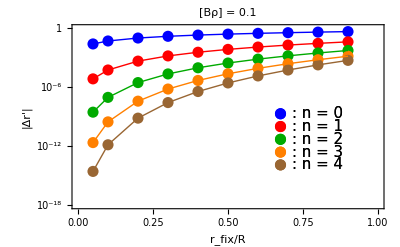

```mathematica
(*Making Plot of radial kick of each order at several radius*)

GList[1]={{{0.8,2*10^-9}},{{0.8,1*10^-10}},{{0.8,5*10^-12}},{{0.8,2.5*10^-13}},{{0.8,1.25*10^-14}}};

TheoComf[1]=Show[
ListLogPlot[Table[TheoToRK1[1,i],{i,1,10}],PlotRange->{{0,1},{0.000000000000000001,1}},FrameLabel->{"r_fix/R","|Δr'|"},ImageSize->{400,320},LabelStyle->Directive[18],Frame->True,Axes->None,PlotStyle->{Blue,PointSize[0.02]},PlotLabel->Style["[Bρ] = 0.1",18]],
ListLogPlot[Table[TheoToRK2[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red,PointSize[0.02]}],
ListLogPlot[Table[TheoToRK3[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Darker[Green],PointSize[0.02]}],
ListLogPlot[Table[TheoToRK4[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Orange,PointSize[0.02]}],
ListLogPlot[Table[TheoToRK5[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Brown,PointSize[0.02]}],

ListLogPlot[Table[TheoToRK1[1,i],{i,1,10}],PlotRange->{{0,1},{0.000000000000000001,1}},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Blue},Joined->True],
ListLogPlot[Table[TheoToRK2[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red},Joined->True],
ListLogPlot[Table[TheoToRK3[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Darker[Green]},Joined->True],
ListLogPlot[Table[TheoToRK4[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Orange},Joined->True],
ListLogPlot[Table[TheoToRK5[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Brown},Joined->True],

ListLogPlot[GList[1],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{": n = 0",15},{": n = 1",15},{": n = 2",15},{": n = 3",15},{": n = 4",15}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListLogPlot[{{0.675,2*10^-9}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Blue,PointSize[0.02]}],
ListLogPlot[{{0.675,1*10^-10}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Red,PointSize[0.02]}],
ListLogPlot[{{0.675,5*10^-12}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Darker[Green],PointSize[0.02]}],
ListLogPlot[{{0.675,2.5*10^-13}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Orange,PointSize[0.02]}],
ListLogPlot[{{0.675,1.25*10^-14}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Brown,PointSize[0.02]}]
]
```

```mathematica
(*Export graphic data to the directory on your computer:you have to specify the directory where you want to export*)

Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Theory_order_conf_Brho0.1.eps",TheoComf[1],"EPS"];
```